# Diffusion coefficients at fixed sma

```mathematica
col=ColorData[10]/@Range[20]
```

{RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275]}

## Import data

```mathematica
tabj=Import["../../data/Dump_Diffusion_Coefficients_Cut_TH.hf5",{"Datasets","tabj"}];
tabDRRjj=Import["../../data/Dump_Diffusion_Coefficients_Cut_TH.hf5",{"Datasets","tabDRRjj"}]; 

tabDNRjj=Import["../../data/Dump_Diffusion_Coefficients_Cut_TH.hf5",{"Datasets","tabDNRjj"}]; 
DRRjjTable={tabj,tabDRRjj}//Transpose;

DNRjjTable={tabj,tabDNRjj}//Transpose;
```

## Plot data

### SRR diffusion coefficients

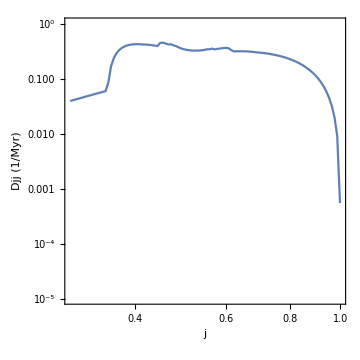

```mathematica
pRRjj=ListPlot[DRRjjTable,PlotRange->{{0.3,1.0},{10^-5,1}},ScalingFunctions->{"Log10","Log10"},Joined->True,InterpolationOrder->1,PlotLegends->Automatic,Frame->True,AspectRatio->1,ImageSize->Medium,FrameLabel->{Style["j",Medium,Bold],Style["Djj (1/Myr)",Medium,Bold]}]
```

### NR diffusion coefficients

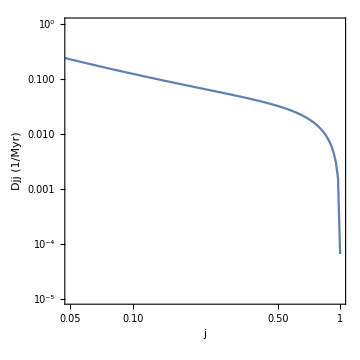

```mathematica
pNRjj=ListPlot[DNRjjTable,PlotRange->{{0.05,1},{10^-5,1}},ScalingFunctions->{"Log10","Log10"},Joined->True,InterpolationOrder->1,PlotLegends->Automatic,Frame->True,AspectRatio->1,ImageSize->Medium,FrameLabel->{Style["j",Medium,Bold],Style["Djj (1/Myr)",Medium,Bold]}]
```

### RR and NR diffusion coefficients together

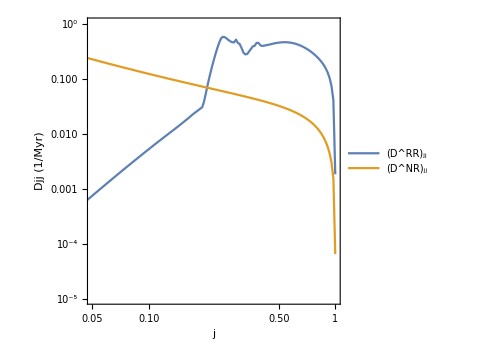

```mathematica
pjj=ListPlot[{DRRjjTable,DNRjjTable},PlotRange->{{0.05,1},{10^-5,1}},ScalingFunctions->{"Log10","Log10"},Joined->True,InterpolationOrder->1,PlotLegends->{"(D^RR)_jj","(D^NR)_jj"},Frame->True,AspectRatio->1,ImageSize->Medium,FrameLabel->{Style["j",Medium,Bold],Style["Djj (1/Myr)",Medium,Bold]}]
```

## Save data

### Both RR and NR diffusion coefficients together

```mathematica
Export["../../graphs/Mathematica/DjjCut.png",pjj]
```

../../graphs/Mathematica/DjjCut.png